# Linear Rayleigh--Taylor Initial-Value Problem with Finite Vertical Walls

This notebook solves the linear hydrodynamic Rayleigh--Taylor initial-value problem for a flat interface with an imposed initial vertical perturbation velocity at the interface.

The interface is z = 0. The upper wall of fluid 1 with density rho1 is z = H1 and the lower wall is z = -H2, with H1 > 0 and H2 > 0. The interface displacement is eta(x,t), with eta(x,0) = 0 and eta_t(x,0) = v0(x).

Corrections in this version:
1. The dispersion relation uses the capillary sign omega2[k] = (k (rho1-rho2) g - sigma k^3)/(rho1 Coth[k H1] + rho2 Coth[k H2]).
2. No NIntegrate is used in the default workflow. Fourier coefficients are computed by a periodic trapezoidal rule, which removes the NIntegrate::itraw and NIntegrate::ncvb messages caused by residual symbolic/numerical iterator conflicts.
3. The first cell uses Remove["Global`*"] so that old memoized definitions from previous evaluations are eliminated.

## 1. Clear the workspace and define physical parameters.

```mathematica
(* Geometry:
   upper fluid: 0 < z < H1
   lower fluid: -H2 < z < 0
   interface: z = 0
*)

pars = {
   rho1 -> 2.0,
   rho2 -> 1.0,
   g -> 9.81,
   sigma -> 0.01,
   H1 -> 1.0,
   H2 -> 1.0,
   L -> 2 Pi
};

Lnum = N[L /. pars];
```

## 2. Dispersion relation. For positive depths H1 and H2, the finite-depth dispersion relation used here is omega2(k) = (k (rho1-rho2) g - sigma k^3)/(rho1 Coth[k H1] + rho2 Coth[k H2]). The sign of the capillary term is the corrected sign supplied by the user. For rho1 > rho2, long waves are unstable and sufficiently short waves are stabilized by surface tension.

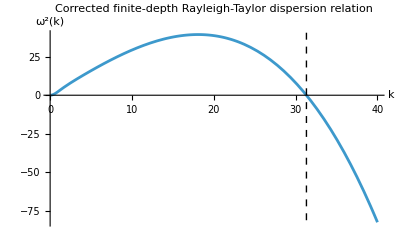

```mathematica
omega2[k_] := (k (rho1 - rho2) g - sigma k^3)/
              (rho1 Coth[k H1] + rho2 Coth[k H2]);

omega2Num[k_?NumericQ] := N[omega2[k] /. pars];

kCritical = Sqrt[((rho1 - rho2) g)/sigma] /. pars;

Plot[
  omega2Num[k],
  {k, 0.05, 40},
  AxesLabel -> {"k", "\!\(\*SuperscriptBox[\(ω\), \(2\)]\)(k)"},
  PlotRange -> All,
  Epilog -> {Dashed, Line[{{kCritical, -10^4}, {kCritical, 10^4}}]},
  PlotLabel -> "Corrected finite-depth Rayleigh-Taylor dispersion relation"
]
```

## 3. Time propagator for each Fourier mode. Each Fourier mode satisfies eta_k''(t) = omega2(k) eta_k(t). With eta_k(0)=0 and eta_k'(0)=vHat_k, eta_k(t) = vHat_k Sinh[Sqrt[omega2(k)] t]/Sqrt[omega2(k)]. If omega2(k) < 0, this expression is equivalent to the usual oscillatory formula involving Sin[Sqrt[-omega2(k)] t].

```mathematica
tol = 10^-12;

growthKernel[lambda_?NumericQ, t_?NumericQ] :=
  If[Abs[lambda] < tol,
     t,
     Sinh[Sqrt[lambda] t]/Sqrt[lambda]
  ];

growthKernelDot[lambda_?NumericQ, t_?NumericQ] :=
  If[Abs[lambda] < tol,
     1,
     Cosh[Sqrt[lambda] t]
  ];
```

## 4. Initial vertical perturbation velocity at the interface. The example below is periodic on [0,L]. The symbolic expression v0Expr is only used to define the numerical function v0. The Fourier projection below does not use symbolic integration.

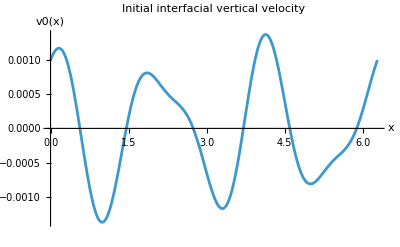

```mathematica
U0 = 10^-3;

v0Expr = U0 Cos[3 x] + (2/5) U0 Sin[5 x];

v0[xVal_?NumericQ] := N[v0Expr /. x -> xVal];

Plot[
  v0[x],
  {x, 0, Lnum},
  AxesLabel -> {"x", "v0(x)"},
  PlotLabel -> "Initial interfacial vertical velocity"
]
```

## 5. Fourier coefficients without NIntegrate. The coefficient convention is vHat[n] = (1/L) Integral_0^L v0(x) Exp[-I k_n x] dx, k_n = 2 Pi n/L. To avoid NIntegrate errors during Plot, the integral is approximated by the periodic trapezoidal rule. This is spectrally accurate for smooth periodic functions and exact up to roundoff for the present trigonometric polynomial if nSamples is sufficiently large.

```mathematica
nMax = 32;

kn[n_Integer] := 2 Pi n/Lnum;

modes = Join[Range[-nMax, -1], Range[1, nMax]];

nSamples = 4096;

xGrid = N[Lnum Range[0, nSamples - 1]/nSamples];
v0Grid = v0 /@ xGrid;

Clear[vHat];

vHat[n_Integer] := vHat[n] =
  Chop[
    (1/nSamples) Total[v0Grid Exp[-I kn[n] xGrid]],
    10^-14
  ];

Table[
  {n, kn[n], vHat[n]},
  {n, -6, 6}
]
```

{{-6,-6.,0},{-5,-5.,0.+0.0002 ⅈ},{-4,-4.,0},{-3,-3.,0.0005},{-2,-2.,0},{-1,-1.,0},{0,0.,0},{1,1.,0},{2,2.,0},{3,3.,0.0005},{4,4.,0},{5,5.,0.-0.0002 ⅈ},{6,6.,0}}

## 6. Reconstruct the interface displacement eta(x,t) and the interfacial velocity eta_t(x,t). All summations are evaluated numerically. The real part is taken because the physical perturbation is real-valued.

```mathematica
etaHat[n_Integer, tVal_?NumericQ] :=
  vHat[n] growthKernel[omega2Num[Abs[kn[n]]], tVal];

eta[xVal_?NumericQ, tVal_?NumericQ] :=
  Re[
    Total[
      etaHat[#, tVal] Exp[I kn[#] xVal] & /@ modes
    ]
  ];

wInterfaceHat[n_Integer, tVal_?NumericQ] :=
  vHat[n] growthKernelDot[omega2Num[Abs[kn[n]]], tVal];

wInterface[xVal_?NumericQ, tVal_?NumericQ] :=
  Re[
    Total[
      wInterfaceHat[#, tVal] Exp[I kn[#] xVal] & /@ modes
    ]
  ];
```

## 7. Verify eta(x,0)=0 and eta_t(x,0)=v0(x). This cell no longer calls NIntegrate. If NIntegrate messages still appear, the kernel still contains old definitions; evaluate the first cell again or choose Evaluation > Quit Kernel > Local, then evaluate the notebook from the beginning.

```mathematica
Plot[
  Evaluate[{eta[x, 0], wInterface[x, 0], v0[x]}],
  {x, 0, Lnum},
  PlotLegends -> {"eta(x,0)", "eta_t(x,0)", "v0(x)"},
  AxesLabel -> {"x", "amplitude"},
  PlotLabel -> "Verification of the initial conditions"
]
```

Plot::nonopt: Options expected (instead of {x,0,Lnum}) beyond position 2 in Plot[{eta[x,0],wInterface[x,0]},v0[x],{x,0,Lnum},PlotLegends→{eta(x,0),eta_t(x,0),v0(x)},AxesLabel→{x,amplitude},PlotLabel→Verification of the initial conditions]. An option must be a rule or a list of rules.

Plot[{eta[x,0],wInterface[x,0]},v0[x],{x,0,Lnum},PlotLegends→{eta(x,0),eta_t(x,0),v0(x)},AxesLabel→{x,amplitude},PlotLabel→Verification of the initial conditions]

A numerical error check is often clearer than a plot.

```mathematica
checkGrid = N[Lnum Range[0, 512]/512];

maxEtaInitialError =
  Max[Abs[eta[#, 0] & /@ checkGrid]];

maxVelocityInitialError =
  Max[Abs[(wInterface[#, 0] - v0[#]) & /@ checkGrid]];

{maxEtaInitialError, maxVelocityInitialError}
```

{0.,3.46945×10^-18}

## 8. Vertical velocity fields in the two fluids. The vertical shape functions satisfy w1(H1)=0 and w2(-H2)=0, while w1(0)=w2(0)=eta_t(x,t).

```mathematica
shape1[k_?NumericQ, zVal_?NumericQ] :=
  Sinh[k ((H1 /. pars) - zVal)]/Sinh[k (H1 /. pars)];

shape2[k_?NumericQ, zVal_?NumericQ] :=
  Sinh[k (zVal + (H2 /. pars))]/Sinh[k (H2 /. pars)];

w1[xVal_?NumericQ, zVal_?NumericQ, tVal_?NumericQ] :=
  Re[
    Total[
      (wInterfaceHat[#, tVal] shape1[Abs[kn[#]], zVal] Exp[I kn[#] xVal]) & /@ modes
    ]
  ];

w2[xVal_?NumericQ, zVal_?NumericQ, tVal_?NumericQ] :=
  Re[
    Total[
      (wInterfaceHat[#, tVal] shape2[Abs[kn[#]], zVal] Exp[I kn[#] xVal]) & /@ modes
    ]
  ];
```

## 9. Verify the impermeability conditions at the walls.

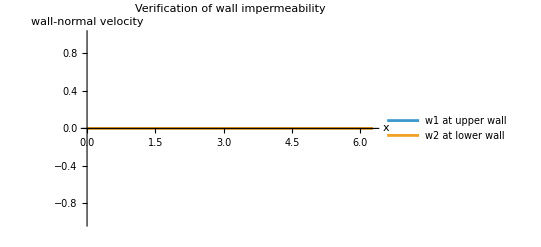

```mathematica
Plot[
  Evaluate[
    {
      w1[x, H1 /. pars, 0],
      w2[x, -(H2 /. pars), 0]
    }
  ],
  {x, 0, Lnum},
  PlotLegends -> {"w1 at upper wall", "w2 at lower wall"},
  AxesLabel -> {"x", "wall-normal velocity"},
  PlotLabel -> "Verification of wall impermeability"
]
```

```mathematica
maxUpperWallError =
  Max[Abs[w1[#, H1 /. pars, 0] & /@ checkGrid]];

maxLowerWallError =
  Max[Abs[w2[#, -(H2 /. pars), 0] & /@ checkGrid]];

{maxUpperWallError, maxLowerWallError}
```

{0.,0.}

## 10. Interface evolution.

```mathematica
tMax = 1.0;

Plot3D[
  eta[x, t],
  {x, 0, Lnum},
  {t, 0, tMax},
  AxesLabel -> {"x", "t", "η(x,t)"},
  PlotRange -> All,
  Mesh -> None,
  PlotLabel -> "Interface displacement eta(x,t)"
]
```

-Graphics3D-

## 11. Single-mode analytical check. For v0(x)=U0Single Cos[k0 x], the solution reduces to a single Fourier mode.

```mathematica
ClearAll[etaSingle, wInterfaceSingle, w1Single, w2Single, kernel];

kernel[lambda_, t_] :=
  Piecewise[
    {
      {t, lambda == 0}
    },
    Sinh[Sqrt[lambda] t]/Sqrt[lambda]
  ];

k0 = 3;
U0Single = 10^-3;

etaSingle[x_, t_] :=
  U0Single kernel[omega2[k0], t] Cos[k0 x];

wInterfaceSingle[x_, t_] :=
  D[etaSingle[x, t], t];

w1Single[x_, z_, t_] :=
  wInterfaceSingle[x, t] Sinh[k0 (H1 - z)]/Sinh[k0 H1];

w2Single[x_, z_, t_] :=
  wInterfaceSingle[x, t] Sinh[k0 (z + H2)]/Sinh[k0 H2];

FullSimplify[
  {
    etaSingle[x, 0],
    D[etaSingle[x, t], t] /. t -> 0,
    w1Single[x, H1, t],
    w2Single[x, -H2, t]
  }
]
```

{0,Cos[3 x]/1000,0,0}

The expected result is {0, U0Single Cos[k0 x], 0, 0}.